```mathematica
(*Complete model with stiffness*)
arraysize=2700;
sol[x_,l_,b_,c_,l1_]:=Assuming[{l>0,b>0,x>0,c>0,l1>0},Integrate[c/l/(x-y)^b(1-Exp[-Abs[x-y]/ l1]),{y,-l,0}]]
FullSimplify[sol[x,l,b,c,l1]]
Limit[FullSimplify[sol[x,l,b,c,l1]],l->0]
```

(c (((x (l+x))^-b (-x^b (l+x)+x (l+x)^b))/(-1+b)+l1^(1-b) (-Gamma[1-b,x/l1]+Gamma[1-b,(l+x)/l1])))/l

c (-ⅇ^(-x/l1) l1^-b (x/l1)^-b+x^b (x^2)^-b)

```mathematica
(c (((x (l+x))^-b (-x^b (l+x)+x (l+x)^b))/(-1+b)+l1^(1-b) (-Gamma[1-b,x/l1]+Gamma[1-b,(l+x)/l1])))/l
```

(c (((x (l+x))^-b (-x^b (l+x)+x (l+x)^b))/(-1+b)+l1^(1-b) (-Gamma[1-b,x/l1]+Gamma[1-b,(l+x)/l1])))/l

```mathematica
(*Data importation and fit*)
dataDamID=Import[StringJoin[NotebookDirectory[],"log10binnning.bin0.1.LIMIT1000000.SHIFT0.MIN1000.DamID_0.1nm1nm_allmerged.w1500000.e0.lb.files.dat"]];
data4C=Import[StringJoin[NotebookDirectory[],"log10binnning.bin0.1.LIMIT1000000.SHIFT0.MIN1000.4C_allmerged.w1500000.e0.lb.files.dat"]];
model[x_,l_,b_,c_,l1_]=sol[x,l,b,c,l1];
nlmDamID=NonlinearModelFit[dataDamID,{model[x,arraysize,0.92,c,l1],c>1,l1>1000},{c,l1},x];
nlmDamID["ParameterTable"]
nlmDamID["AdjustedRSquared"]
nlm4C=NonlinearModelFit[data4C,{model[x,arraysize,0.85,c,l1],c>1,l1>1000},{c,l1},x];
nlm4C["ParameterTable"]
nlm4C["AdjustedRSquared"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
c | 2169.45 | 88.3716 | 24.5492 | 5.94663×10^-21
l1 | 2424.57 | 209.273 | 11.5856 | 2.11725×10^-12

0.992371

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
c | 1414.16 | 30.8892 | 45.7818 | 1.34257×10^-28
l1 | 3119.32 | 130.919 | 23.8263 | 1.35988×10^-20

0.997755

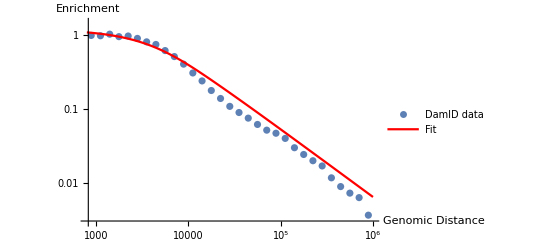

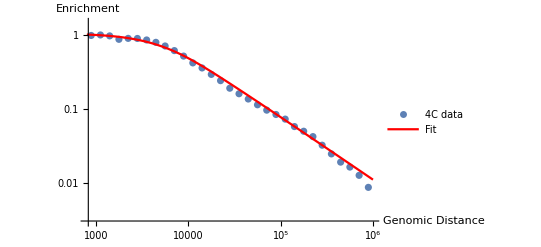

```mathematica
plot1 = Show[ListLogLogPlot[dataDamID,PlotStyle->Grey,PlotLegends->{"DamID data"},AxesLabel->{"Genomic Distance","Enrichment"},PlotRange->{{800,1000000},{0.003,1.5}}],LogLogPlot[nlmDamID[x],{x,800,1000000},PlotStyle->Red,PlotLegends->{"Fit"},PlotRange->All]]

plot2=Show[ListLogLogPlot[data4C,PlotStyle->Grey,PlotLegends->{"4C data"},AxesLabel->{"Genomic Distance","Enrichment"},PlotRange->{{800,1000000},{0.003,1.5}}],LogLogPlot[nlm4C[x],{x,800,1000000},PlotStyle->Red,PlotLegends->{"Fit"},PlotRange->All]]
```

```mathematica
(*Without stiffness model*)
sol[x_,l_,b_,c_]:=Assuming[{l>0,b>0,x>0,c>0},Integrate[c/l/(x-y)^b(1),{y,-l,0}]]
FullSimplify[sol[x,l,b,c]]
Limit[FullSimplify[sol[x,l,b,c]],l->0]
model[x_,l_,b_,c_]=sol[x,l,b,c];
nlmDamID=NonlinearModelFit[dataDamID,{model[x,arraysize,0.91,c],c>100},c,x];
nlmDamID["ParameterTable"]
nlmDamID["AdjustedRSquared"]
nlm4C=NonlinearModelFit[data4C,{model[x,arraysize,0.85,c],c>100},c,x];
nlm4C["ParameterTable"]
nlm4C["AdjustedRSquared"]
```

(c (x (l+x))^-b (-x^b (l+x)+x (l+x)^b))/((-1+b) l)

c x^b (x^2)^-b

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
c | 1336.63 | 58.235 | 22.9523 | 1.38749×10^-20

0.944326

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
c | 850.058 | 41.066 | 20.6998 | 2.57338×10^-19

0.932385

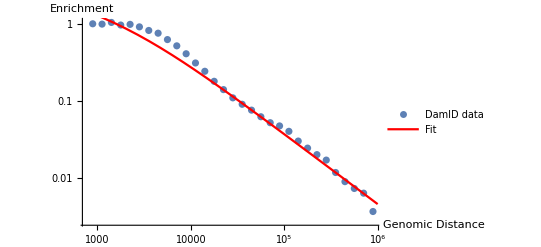

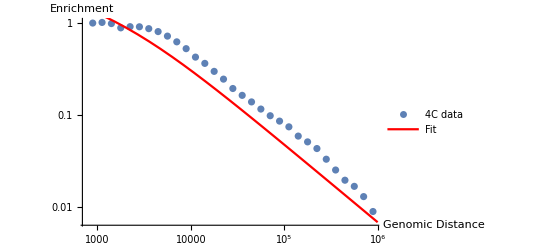

```mathematica
plot3=Show[ListLogLogPlot[dataDamID,PlotStyle->Grey,PlotLegends->{"DamID data"},PlotRange->All,AxesLabel->{"Genomic Distance","Enrichment"}],LogLogPlot[nlmDamID[x],{x,1,1000000},PlotStyle->Red,PlotLegends->{"Fit"},PlotRange->All]]

plot4=Show[ListLogLogPlot[data4C,PlotStyle->Grey,PlotLegends->{"4C data"},PlotRange->All,AxesLabel->{"Genomic Distance","Enrichment"}],LogLogPlot[nlm4C[x],{x,1,1000000},PlotStyle->Red,PlotLegends->{"Fit"},PlotRange->All]]
```